# Load first-order Lorenz gauge metric perturbation data from the h1Lorenz code

This notebook uses SimulationTools which you can download from: https://simulationtools.org/

```mathematica
<<SimulationTools`
```

The mass of the primary is set to 1

```mathematica
M=1;
```

## Define function Loadh1Data[r0,l,m] to load the h1 data

```mathematica
fieldOrder[l_,m_]/;EvenQ[l+m]:=If[m==0,{1,3,5,6,7,2,4},{1,3,5,6,7,2,4}]
fieldOrder[0,0]:={1,3,6,2}
fieldOrder[1,0]:={9,8}
fieldOrder[1,1]:={1,3,5,6,2,4}
fieldOrder[l_,m_]/;OddQ[l+m]:=If[m==0,{9,10,8},{9,10,8}]
```

```mathematica
Loadh1Data[r0_,l_,m1_]:=Module[{gridJ, r0PosJ, tmp,m=m1,fields,C∞Data,CHData,fileName},
SetDirectory[NotebookDirectory[]<>"../data/fields_r"<>ToString[r0]];

fileName="h1-l"<>ToString[l]<>"m"<>ToString[m1]<>".h5";

gridJ=ImportHDF5[fileName,{"Datasets","/grid"}];
r0PosJ=Position[gridJ,N[r0]][[1,1]];
gridJ=Insert[gridJ,N[r0],r0PosJ+1];

fields=fieldOrder[l,m1];

tmp=Map[Flatten,Transpose@{gridJ,Join[ImportHDF5["h1-l"<>ToString[l]<>"m"<>ToString[m1]<>".h5",{"Datasets","inhom_left"}],ImportHDF5["h1-l"<>ToString[l]<>"m"<>ToString[m1]<>".h5",{"Datasets","inhom_right"}]]}];
Do[h1[r0][fields[[j]],l,m]=ToDataTable[Table[{tmp[[k,1]],tmp[[k,2+4(j-1)]]+I tmp[[k,3+4(j-1)]]},{k,1,Length[gridJ]}]],{j,1,Length[fields]}];
Do[drh1[r0][fields[[j]],l,m]=ToDataTable[Table[{tmp[[k,1]],tmp[[k,4+4(j-1)]]+I tmp[[k,5+4(j-1)]]},{k,1,Length[gridJ]}]],{j,1,Length[fields]}];

C∞Data=#[[1]]+I#[[2]]&/@ArrayReshape[Import[fileName,{"Datasets","/C_inf"}],{If[EvenQ[l+m],5,2],2}];
CHData=#[[1]]+I#[[2]]&/@ArrayReshape[Import[fileName,{"Datasets","/C_horiz"}],{If[EvenQ[l+m],5,2],2}];

Do[
C∞[r0][fields[[j]],l,m]=C∞Data[[j]];
CH[r0][fields[[j]],l,m]=CHData[[j]],
{j,1,If[EvenQ[l+m],5,2]}
]
]
```

## Example of loading and plotting the data

```mathematica
Loadh1Data[6,2,2]
Loadh1Data[6,2,1]
```

After you use Loadh1Data you can find the data in h1[r0][i,l,m] and drh1[r0][i,l,m]

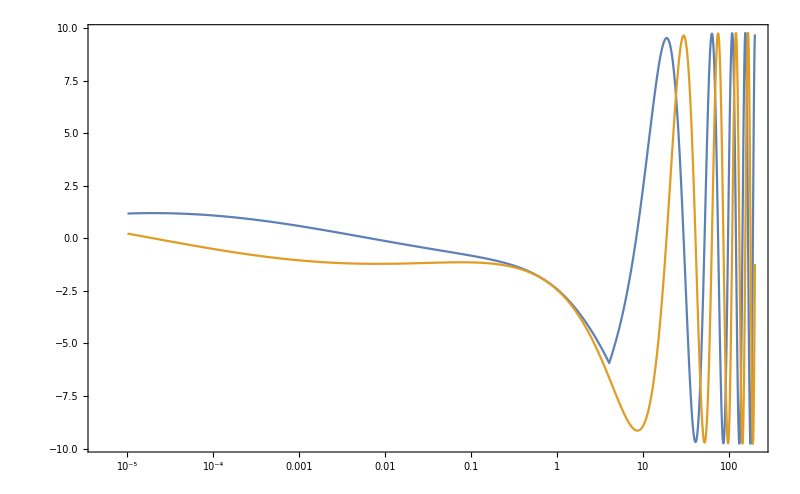

```mathematica
ListLogLinearPlot[Shifted[Slab[h1[6][7,2,2],2;;200],-2]//ReIm,Joined->True,ImageSize->800,PlotTheme->"Detailed",PlotRange->All]
```

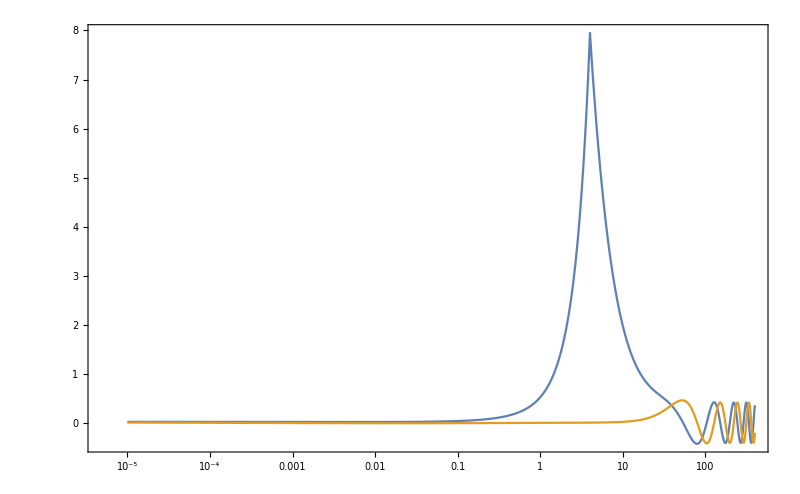

```mathematica
ListLogLinearPlot[Shifted[Slab[h1[6][8,2,1],2;;400],-2]//ReIm,Joined->True,ImageSize->800,PlotTheme->"Detailed",PlotRange->All]
```

To get the radial values of the data use, e.g.,

```mathematica
ToListOfCoordinates[h1[6][1,2,2]];
```

To get a regular list of the data use, e.g.,

```mathematica
ToList[h1[6][1,2,2]];
```

## Load the asymptotic values of the field

The Loadh1Data function also created C∞ and CH functions

Flux formula from Eq. (75) of https://arxiv.org/abs/1012.5860

```mathematica
FluxLorenz[l_,m_]:=With[{r0=6},(ω^2 Abs[C∞[r0][If[EvenQ[l+m],7,10],l,m]]^2)/(64π (l-1)l(l+1)(l+2))//.{ω->m Ω,Ω->r0^(-3/2)}]
```

```mathematica
<<Teukolsky`
```

```mathematica
orbit=KerrGeoOrbit[0,6`32,0,1];
```

```mathematica
With[{l=2},Do[modeT[l,m]=TeukolskyPointParticleMode[-2,l,m,0,0,orbit],{m,1,l}]];
```

```mathematica
With[{l=2},Table[1-FluxLorenz[2,m]/modeT[2,m]["Fluxes"]["Energy"]["ℐ"],{m,1,l}]]
```

{8.46844×10^-11,1.7559×10^-10}